```mathematica
x = 1;
```

```mathematica
y = x;
```

```mathematica
z:=x;
```

```mathematica
Print[x]
```

1

```mathematica
Print[y]
```

1

```mathematica
Print[z]
```

1

```mathematica
x = 2;
```

```mathematica
Print[x]
```

2

```mathematica
Print[y]
```

1

```mathematica
Print[z]
```

2

```mathematica
silnia[0]= 1;
```

```mathematica
silnia[n_]:=silnia[n - 1]n;
```

```mathematica
silnia[10]
```

3628800

```mathematica
Factorial[10]
```

3628800

```mathematica
silnia[2]
```

2

```mathematica
Hold[FullForm[x = 1]]
```

Hold[Set[x,1]]

```mathematica
x = 1;
```

```mathematica
{x , y , z} = {1 , 2 , 3};
```

```mathematica
x
```

1

```mathematica
y
```

2

```mathematica
z
```

3

```mathematica
Hold[FullForm[z:=x]]
```

Hold[SetDelayed[z,x]]

```mathematica
Hold[FullForm[{1 , 2 , 3}]]
```

Hold[List[1,2,3]]

```mathematica
Head[List[1,2,3]]
```

List

```mathematica
(*to jest komentarz*)
```

```mathematica
(*"https://kacpertopol.github.io/"*)
```

```mathematica
covidData = Import["https://github.com/CSSEGISandData/COVID-19/raw/master/csse_covid_19_data/csse_covid_19_time_series/time_series_covid19_confirmed_global.csv"];
```

```mathematica
simpleData = {{132 , 321 , 111},{222 , 333 , 444},{534 ,934},{342 , 745 , 234}};
```

```mathematica
Length[simpleData]
```

4

```mathematica
Dimensions[simpleData]
```

{4}

```mathematica
Length[{1 , 2 , 3 , 4}]
```

4

```mathematica
Length[mojalista[1 , 2 , 3]]
```

3

```mathematica
Length[aaa[bbb[ccc],ddd]]
```

2

```mathematica
(*Part [[]]*)
```

```mathematica
{1 , 2 , 3 , 4 , 5}[[2]]
```

2

```mathematica
{1 , 2 , 3 , 4 , 5}[[2;;4]]
```

{2,3,4}

```mathematica
{1 , 2 , 3 , 4 , 5}[[2;;]]
```

{2,3,4,5}

```mathematica
{1 , 2 , 3 , 4 , 5}[[;;4]]
```

{1,2,3,4}

```mathematica
{1 , 2 , 3 , 4 , 5}[[-1]]
```

5

```mathematica
{1 , 2 , 3 , 4 , 5}[[-2]]
```

4

```mathematica
{1 , 2 , 3 , 4 , 5}[[-3;;]]
```

{3,4,5}

```mathematica
Hold[FullForm[{1 , 2 , 3 , 4 , 5}[[-2;;]]]]
```

Hold[Part[List[1,2,3,4,5],Span[-2,All]]]

```mathematica
aaa[bbb[ccc] , ddd][[1]]
```

bbb[ccc]

```mathematica
aaa[bbb[ccc] , ddd][[2]]
```

ddd

```mathematica
aaa[bbb[ccc] , ddd][[1]][[1]]
```

ccc

```mathematica
bbb[ccc][[0]]
```

bbb

```mathematica
Head[bbb[ccc]]
```

bbb

```mathematica
Hold[FullForm[{1 , 2 , 3}]]
```

Hold[List[1,2,3]]

```mathematica
mojaLista = {1 , 2,3};
```

```mathematica
Print[mojaLista]
```

{1,2,3}

```mathematica
FullForm[mojaLista]
```

List[1,2,3]

```mathematica
covidData//Length
```

290

```mathematica
Length[covidData]
```

290

```mathematica
covidData//Dimensions
```

{290,999}

```mathematica
covidDataData = covidData[[2;;,5;;]];
```

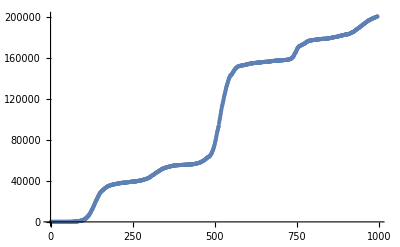

```mathematica
ListPlot[covidDataData[[1]]]
```

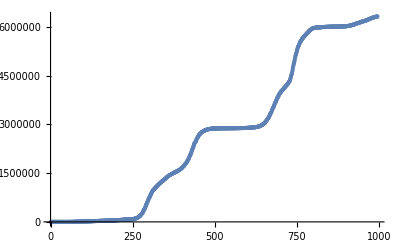

```mathematica
ListPlot[Cases[covidData , {_,"Poland" , _ , _,__}][[1,5;;]]]
```

```mathematica
(*CTRL + 6 x^n*)
```

```mathematica
Hold[FullForm[n^m]]
```

Hold[Power[n,m]]

```mathematica
Power[n , m]
```

n^m

```mathematica
Clear[x , y , z]
```

```mathematica
FullSimplify[1 + 2 x + x^2]
```

(1+x)^2

```mathematica
Simplify[1 + 2 x + x^2]
```

(1+x)^2

```mathematica
(*- >*)
```

```mathematica
FullSimplify[x + 1 > 0 , Assumptions-> x>0]
```

True

```mathematica
FullSimplify[x + 1 > 0 , x>0]
```

True

```mathematica
f[x_ , y_]:=If[x^2+y^2< (3/4)^2 , 1 , 0];
```

```mathematica
f[3 , 4]
```

0

```mathematica
f[0.15 , 0.15]
```

1

```mathematica
True&&True
```

True

```mathematica
True&&False
```

False

```mathematica
True||False
```

True

```mathematica
False||False
```

False

```mathematica
(**)
```

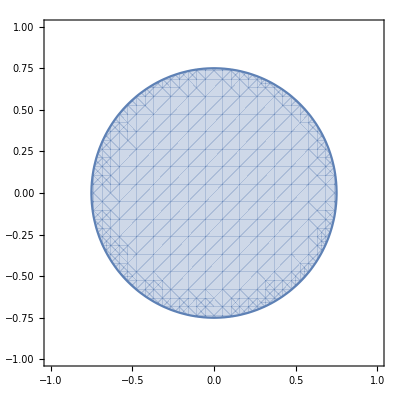

```mathematica
RegionPlot[f[x , y]===1 , {x , -1 , 1} , {y , -1 , 1}]
```

```mathematica
l == r
```

l==r

```mathematica
l===r
```

False

```mathematica
l === l
```

True

```mathematica
Integrate[f[x , y] , {x , -1 , 1} , {y , -1 , 1}]
```

(9 π)/16

```mathematica
(*ESC nazwa ESC*)
```

```mathematica
π (3/4)^2
```

(9 π)/16

```mathematica
N[π (3/4)^2]
```

1.76715